## Get the Data

```mathematica
GE0data=Import["~/Research/SIR/Source/FRO_adm0.kmz","Data"];
```

```mathematica
GE1data=Import["~/Research/SIR/Source/FRO_adm1.kmz","Data"];
```

```mathematica
GE2data=Import["~/Research/SIR/Source/FRO_adm1.kmz","Data"];
```

```mathematica
names0=Flatten["PlacemarkNames"/.GE0data]
```

{Faroe Islands}

```mathematica
names1= Flatten["PlacemarkNames"/.GE1data]
```

{Eysturoyar,Norderøerne,Sandoyar,Streymoyar,Suðuroyar,Vågø}

```mathematica
names2=Flatten["PlacemarkNames"/.GE2data]
```

{Eysturoyar,Norderøerne,Sandoyar,Streymoyar,Suðuroyar,Vågø}

```mathematica
(Geom0=Flatten["Geometry"/.GE0data])//Length
```

26

```mathematica
(Geom1=Flatten["Geometry"/.GE1data])//Length
```

27

```mathematica
(Geom2=Flatten["Geometry"/.GE2data])//Length
```

27

```mathematica
gdata0=SortBy[Geom0,Length@#[[1,1]]&]//Reverse;
```

```mathematica
gdata1=SortBy[Geom2,Length@#[[1,1]]&]//Reverse;
```

```mathematica
gdata2=SortBy[Geom3,Length@#[[1,1]]&]//Reverse;
```

```mathematica
Grid[Thread[{gdata1,gdata2}],Frame->All]
```

Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]

```mathematica
names=Range[8]/.{1->"Esturoy",2->"Bordoy",3-> "Suduroy",4->"Streymoy",5->"Vagar",6->"Sandoy",7->"Kalsoy",8->"Svinoy"}
```

{Esturoy,Bordoy,Suduroy,Streymoy,Vagar,Sandoy,Kalsoy,Svinoy}

```mathematica
pops = {"Streymoy"->22450,"Esturoy"->10726,"Vagar"-> 3064,"Suduroy"->4680,"Sandoy"->1283,"Bordoy"-> 4940+596+129,"Kalsoy"-> 94, "Svinoy"->32}
```

{Streymoy→22450,Esturoy→10726,Vagar→3064,Suduroy→4680,Sandoy→1283,Bordoy→5665,Kalsoy→94,Svinoy→32}

```mathematica
pops = {"Streymoy"->50,"Esturoy"->26,"Vagar"-> 34,"Suduroy"->10,"Sandoy"->12,"Bordoy"-> 4+9,"Kalsoy"-> 4, "Svinoy"->2}
```

{Streymoy→50,Esturoy→26,Vagar→34,Suduroy→10,Sandoy→12,Bordoy→13,Kalsoy→4,Svinoy→2}

```mathematica
card={"Esturoy"->1,"Bordoy"->2,"Suduroy"->3,"Streymoy"->4,"Vagar"->5,"Sandoy"->6,"Kalsoy"->7,"Svinoy"->8}
```

{Esturoy→1,Bordoy→2,Suduroy→3,Streymoy→4,Vagar→5,Sandoy→6,Kalsoy→7,Svinoy→8}

```mathematica
Graphics[MapThread[Tooltip[#1,Grid[{{#2,#3}},Frame->All]]&,{gdata2[[;;8]],names,names/.pops}]]
```

-Graphics-

```mathematica
Total[names/.pops]
```

47994

```mathematica
Min[xmin]
```

-7.46667

```mathematica
Max[xmax]
```

-6.28385

## Simply Scale Everything

```mathematica
gxmin = Min[xmin]
```

-7.46667

```mathematica
gxmax = Max[xmax]
```

-6.28385

```mathematica
gymin=Min[ymin]
```

61.3937

```mathematica
gymax=Max[ymax]
```

62.3917

### Bounding Box

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Max[xmax],Max[ymax]}]
```

106.316 mi

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Max[xmax],Min[ymin]}]
```

81.28 mi

```mathematica
GeoDistance[{Min[xmin],Max[ymax]},{Max[xmax],Max[ymax]}]
```

81.28 mi

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Min[xmin],Max[ymax]}]
```

68.4452 mi

```mathematica
GeoDistance[{Max[xmax],Min[ymin]},{Max[xmax],Max[ymax]}]
```

68.6147 mi

```mathematica
{gxmin->5,gxmax->5+81.28,gymin->5,gymax->5+68.6147}
```

{-7.46667→5,-6.28385→86.28,61.3937→5,62.3917→73.6147}

```mathematica
XTransform[x_]:=(x-gxmin)*81.28+5
```

```mathematica
XTransform[gxmax]
```

101.139

```mathematica
YTransform[y_]:=(y-gymin)*68.6147+5
```

```mathematica
YTransform[gymax]
```

73.4718

## Export

```mathematica
xmin=XTransform/@Map[Min[#[[1,1,All,2]]]&,gdata2[[;;8]]]
```

{23.288,66.341,42.8037,21.637,5.,46.8676,57.705,90.344}

```mathematica
xmax=XTransform/@Map[Max[#[[1,1,All,2]]]&,gdata2[[;;8]]]
```

{75.4004,91.3177,70.1933,64.7323,37.6813,72.691,70.7013,101.139}

```mathematica
ymin=YTransform/@Map[Min[#[[1,1,All,1]]]&,gdata2[[;;8]]]
```

{50.3142,58.0336,5.,42.3093,48.0271,29.587,62.0359,62.4649}

```mathematica
ymax=YTransform/@Map[Max[#[[1,1,All,1]]]&,gdata2[[;;8]]]
```

{69.8982,73.4718,22.7256,62.8824,57.4617,40.737,72.1853,67.6111}

```mathematica
GeneralData=Thread[{Range[8],names,"Island",xmin,xmax,ymin,ymax,names/.pops}]
```

{{1,Esturoy,Island,23.288,75.4004,50.3142,69.8982,26},{2,Bordoy,Island,66.341,91.3177,58.0336,73.4718,13},{3,Suduroy,Island,42.8037,70.1933,5.,22.7256,10},{4,Streymoy,Island,21.637,64.7323,42.3093,62.8824,50},{5,Vagar,Island,5.,37.6813,48.0271,57.4617,34},{6,Sandoy,Island,46.8676,72.691,29.587,40.737,12},{7,Kalsoy,Island,57.705,70.7013,62.0359,72.1853,4},{8,Svinoy,Island,90.344,101.139,62.4649,67.6111,2}}

```mathematica
Export["~/Research/SIR/Source/GeneralData.csv",GeneralData]
```

~/Research/SIR/Source/GeneralData.csv

```mathematica
gdata2[[;;8]][[1]][[1,1]]
```

{{62.338,-6.97865},{62.3375,-6.97708},{62.3375,-6.975},{62.3375,-6.97292},{62.3375,-6.97083},{62.337,-6.96927},{62.3359,-6.96823},{62.3354,-6.96667},1803,{62.3396,-6.98958},{62.3396,-6.9875},{62.3396,-6.98542},{62.3396,-6.98333},{62.3396,-6.98125},{62.3391,-6.97969},{62.338,-6.97865}}
 |  |  |  |

```mathematica
gdataTransform =Map[#[[1,1]]/.{{x_,y_}->{XTransform[y],YTransform[x]}}&,gdata2];
```

```mathematica
gdataTransform[[;;8]]
```

{{{44.6663,69.7911},{44.7933,69.7553},{44.9627,69.7553},{45.132,69.7553},{45.3013,69.7553},{45.4283,69.7194},{45.513,69.648},1804,{43.7773,69.8982},{43.9467,69.8982},{44.116,69.8982},{44.2853,69.8982},{44.4547,69.8982},{44.5817,69.8626},{44.6663,69.7911}},6,{1}}
 |  |  |  |

```mathematica
MapThread[Export[StringJoin["~/Research/SIR/Source/",#1,".csv"],#2]&,{names,gdataTransform[[;;8]]}]
```

{~/Research/SIR/Source/Esturoy.csv,~/Research/SIR/Source/Bordoy.csv,~/Research/SIR/Source/Suduroy.csv,~/Research/SIR/Source/Streymoy.csv,~/Research/SIR/Source/Vagar.csv,~/Research/SIR/Source/Sandoy.csv,~/Research/SIR/Source/Kalsoy.csv,~/Research/SIR/Source/Svinoy.csv}

## Projection

```mathematica
GeoGridPosition[GeoPosition[{-6.60052061080933,62.339584350586}],"Stereographic"]
```

GeoGridPosition[{1.20431,-0.157336},Stereographic]

### Bounding Box

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Max[xmax],Max[ymax]}]
```

106.316 mi

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Max[xmax],Min[ymin]}]
```

81.28 mi

```mathematica
GeoDistance[{Min[xmin],Max[ymax]},{Max[xmax],Max[ymax]}]
```

81.28 mi

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Min[xmin],Max[ymax]}]
```

68.4452 mi

```mathematica
GeoDistance[{Max[xmax],Min[ymin]},{Max[xmax],Max[ymax]}]
```

68.6147 mi

### Distances

```mathematica
distances = Map[UnitConvert[GeoDistance[#[[1]],#[[2]]],"Miles"][[1]]&,Partition[gdata2[[1,1,1]],2,2,1]];
```

## Test

```mathematica
data = Import["~/Research/SIR/Source/Esturoy.csv"];
```

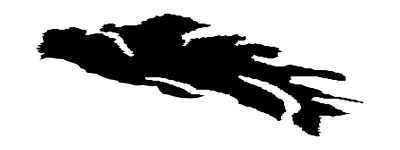

```mathematica
Graphics[Polygon[data]]
```

```mathematica
data = Import["~/Research/SIR/Source/Bordoy.csv"];
```

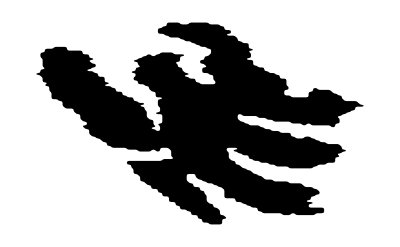

```mathematica
Graphics[Polygon[data]]
```

```mathematica
data = Import["~/Research/SIR/Source/Streymoy.csv"];
```

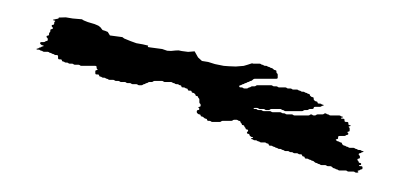

```mathematica
Graphics[Polygon[data]]
```